```mathematica
(* An open boundary stripe.

Modification of the code from this post:
https://mathematica.stackexchange.com/questions/61834/how-to-create-an-hexagonal-lattice-structure
*)
```

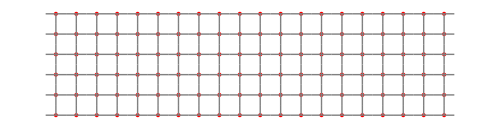

```mathematica
unitCell[x_,y_]:={Red,Disk[{x,y},0.1],Gray,
,Line[{{x,y},{x,y+1/2}}],Line[{{x,y},{x,y-1/2}}],Line[{{x,y},{x+1/2,y}}],Line[{{x,y},{x-1/2,y}}]}
unitCellbdydown[x_,y_]:={Red,Disk[{x,y},0.1],Gray,
,Line[{{x,y},{x+1/2,y}}],Line[{{x,y},{x,y+1/2}}],Line[{{x,y},{x-1/2,y}}]}
unitCellbdyup[x_,y_]:={Red,Disk[{x,y},0.1],Gray,
,Line[{{x,y},{x+1/2,y}}],Line[{{x,y},{x,y-1/2}}],Line[{{x,y},{x-1/2,y}}]}

nline=4;
Graphics[{Block[{unitVectA={0,1},unitVectB={1,0}},Table[unitCell@@(unitVectA j+unitVectB k),{j,1,nline},{k,1,20}]],Block[{unitVectA={0,1},unitVectB={1,0}},Table[unitCellbdydown@@(unitVectA 0+unitVectB k),{k,1,20}]],Block[{unitVectA={0,1},unitVectB={1,0}},Table[unitCellbdyup@@(unitVectA (nline+1)+unitVectB k),{k,1,20}]]},ImageSize->500]
```